```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210224_impacts_in_time_windows"];
```

```mathematica
(* data=Import["data_with_time_windows2.mx"]; *)
```

```mathematica
(* datafullmodified=Import["datafull_manipulated.mx"];
data=Table[Take[datafullmodified,UpTo@i],{i,{46497,91690,138440,183584,230005,275844,320350,367179,413106,459203}}]; *)
```

```mathematica
data=Import["../data/ccm_manipulated_396096_partitioned_in_time_windows.mx",HeaderLines->1];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

Thickness Feature

```mathematica
window=10;
rawaim=data[[window]][[All,10]];
pos=Partition[Flatten@Table[Position[rawaim,i],{i,{"NA",0}}],1];
```

```mathematica
aim=Delete[rawaim,pos];
```

```mathematica
campaign=Delete[data[[window]][[All,2]],pos];
```

```mathematica
seri=Delete[data[[window]][[All,1]],pos];
```

```mathematica
Print["unique aim data members: ",Dimensions@DeleteDuplicates@aim]
Print["aim data length: ",Dimensions@aim]
Print["sequence data groups amount: ",Dimensions@DeleteDuplicates@campaign]
```

unique aim data members: {35}

aim data length: {396096}

sequence data groups amount: {675}

```mathematica
Print["bucket size: ",bucketsize=Ceiling@(N@(Dimensions@aim)/50)]
aimlabeled=Thread[Range@Length@aim->aim];
aimpartitioned=Partition[Normal@Sort@Association@aimlabeled,UpTo@bucketsize];
bins=Table[MinMax[i],{i,Values@aimpartitioned}];
Print["node amount: ",Length@bins];
```

bucket size: {7922}

node amount: 50

```mathematica
Tally@bins
```

{{{41,56},1},{{56,56},1},{{56,57},1},{{57,63},1},{{63,65},1},{{65,65},25},{{65,66},1},{{66,66},2},{{66,67},1},{{67,67},12},{{67,74},1},{{74,76},1},{{76,77},1},{{77,87},1},{{87,87},1}}

```mathematica
repetitives
```

{{65,65},{66,66},{67,67}}

```mathematica
binsrearranged
```

{{41.,56.},{56.,56.},{56.,57.},{57.,63.},{63.,65.},{65.0325,65.0325},{65.065,65.065},{65.0975,65.0975},{65.13,65.13},{65.1625,65.1625},{65.195,65.195},{65.2275,65.2275},{65.26,65.26},{65.2925,65.2925},{65.325,65.325},{65.3575,65.3575},{65.39,65.39},{65.4225,65.4225},{65.455,65.455},{65.4875,65.4875},{65.52,65.52},{65.5525,65.5525},{65.585,65.585},{65.6175,65.6175},{65.65,65.65},{65.6825,65.6825},{65.715,65.715},{65.7475,65.7475},{65.78,65.78},{65.8125,65.8125},{65.,66.},{66.033,66.033},{66.066,66.066},{66.,67.},{67.0335,67.0335},{67.067,67.067},{67.1005,67.1005},{67.134,67.134},{67.1675,67.1675},{67.201,67.201},{67.2345,67.2345},{67.268,67.268},{67.3015,67.3015},{67.335,67.335},{67.3685,67.3685},{67.402,67.402},{67.,74.},{74.,76.},{76.,77.},{77.,87.}}

```mathematica
repetitivesreport=DeleteCases[Tally@bins,x_/;x[[2]]==1];
repetitives=repetitivesreport[[All,1]];
labelgeneration[x_]:=Table[{repetitives[[x]][[1]]+i*repetitives[[x]][[1]]/(2*10^(RealDigits@repetitives[[x]][[1]]+1)[[2]]),repetitives[[x]][[2]]+i*repetitives[[x]][[2]]/(2*10^(RealDigits@repetitives[[x]][[2]]+1)[[2]])},{i,Range@repetitivesreport[[x]][[2]]}]
binsrearranged=N@ReplacePart[bins,Flatten[Table[MapThread[#1->#2&,{Flatten@Position[bins,repetitives[[g]]],labelgeneration[g]}],{g,Range@Length@repetitives}],1]];
```

```mathematica
aimbinned=Values@Sort[Flatten[Table[aimpartitioned[[i]]/.Table[Values@aimpartitioned[[i]][[j]]->binsrearranged[[i]],{j,Length@aimpartitioned[[i]]}],{i,Length@aimpartitioned}],1],#1[[1]]<#2[[1]]&];
Position[aimbinned,Null]
```

{}

```mathematica
aim=aimbinned;
binningmembers=Sort[DeleteDuplicates[aim]];
Print["binning amount: ",Dimensions@DeleteDuplicates@aimbinned]
Print["dimension of binned data: ",Dimensions@aim]
Print["binning members dimension : ",Dimensions@binningmembers]
```

binning amount: {50,2}

dimension of binned data: {396096,2}

binning members dimension : {50,2}

```mathematica
binningmembers=Sort[N@DeleteDuplicates[aim]]
```

{{41.,56.},{56.,56.},{56.,57.},{57.,63.},{63.,65.},{65.,66.},{65.0325,65.0325},{65.065,65.065},{65.0975,65.0975},{65.13,65.13},{65.1625,65.1625},{65.195,65.195},{65.2275,65.2275},{65.26,65.26},{65.2925,65.2925},{65.325,65.325},{65.3575,65.3575},{65.39,65.39},{65.4225,65.4225},{65.455,65.455},{65.4875,65.4875},{65.52,65.52},{65.5525,65.5525},{65.585,65.585},{65.6175,65.6175},{65.65,65.65},{65.6825,65.6825},{65.715,65.715},{65.7475,65.7475},{65.78,65.78},{65.8125,65.8125},{66.,67.},{66.033,66.033},{66.066,66.066},{67.,74.},{67.0335,67.0335},{67.067,67.067},{67.1005,67.1005},{67.134,67.134},{67.1675,67.1675},{67.201,67.201},{67.2345,67.2345},{67.268,67.268},{67.3015,67.3015},{67.335,67.335},{67.3685,67.3685},{67.402,67.402},{74.,76.},{76.,77.},{77.,87.}}

```mathematica
aimbaskets=Values@GroupBy[Thread[{aim,campaign}],Last->First];
aimbasketsrev=Table[DeleteDuplicates[i],{i,aimbaskets}];
Print["binning groups association to count of their total members: ",KeySort@Counts@aim]
Print["binning amount: ",Dimensions@DeleteDuplicates@aim]
```

binning groups association to count of their total members: <|{41.,56.}→7922,{56.,56.}→7922,{56.,57.}→7922,{57.,63.}→7922,{63.,65.}→7922,{65.,66.}→7922,{65.0325,65.0325}→7922,{65.065,65.065}→7922,{65.0975,65.0975}→7922,{65.13,65.13}→7922,{65.1625,65.1625}→7922,{65.195,65.195}→7922,{65.2275,65.2275}→7922,{65.26,65.26}→7922,{65.2925,65.2925}→7922,{65.325,65.325}→7922,{65.3575,65.3575}→7922,{65.39,65.39}→7922,{65.4225,65.4225}→7922,{65.455,65.455}→7922,{65.4875,65.4875}→7922,{65.52,65.52}→7922,{65.5525,65.5525}→7922,{65.585,65.585}→7922,{65.6175,65.6175}→7922,{65.65,65.65}→7922,{65.6825,65.6825}→7922,{65.715,65.715}→7922,{65.7475,65.7475}→7922,{65.78,65.78}→7922,{65.8125,65.8125}→7922,{66.,67.}→7922,{66.033,66.033}→7922,{66.066,66.066}→7922,{67.,74.}→7922,{67.0335,67.0335}→7922,{67.067,67.067}→7922,{67.1005,67.1005}→7922,{67.134,67.134}→7922,{67.1675,67.1675}→7922,{67.201,67.201}→7922,{67.2345,67.2345}→7922,{67.268,67.268}→7922,{67.3015,67.3015}→7922,{67.335,67.335}→7922,{67.3685,67.3685}→7922,{67.402,67.402}→7922,{74.,76.}→7922,{76.,77.}→7922,{77.,87.}→7918|>

binning amount: {50,2}

```mathematica
AbsoluteTiming[singlesupportvalues=Table[N[Count[Table[MemberQ[i,j],{i,aimbasketsrev}],True]/Length[aimbasketsrev]],{j,binningmembers}];]
pairs=Subsets[binningmembers,{2}];
Dimensions[binningmembers]
Dimensions[pairs]
Dimensions[aimbasketsrev]
AbsoluteTiming[pairsupportvalues=Table[N[Count[Table[SubsetQ[i,j],{i,aimbasketsrev}],True]/
Length[aimbasketsrev]],{j,pairs}];]
```

{0.0719329,Null}

{50,2}

{1225,2,2}

{675}

{6.22806,Null}

```mathematica
AbsoluteTiming[liftvalues=pairsupportvalues/(DeleteCases[Flatten@UpperTriangularize[Table[singlesupportvalues[[j]]*singlesupportvalues[[k]],{j,Length[binningmembers]},{k,Length[binningmembers]}],1],0.]);]
```

{0.0051813,Null}

```mathematica
allmatrixelements=Sort[Join[pairs,Reverse[pairs,2],Table[{i,i},{i,binningmembers}]]];
```

{172,2,2}

{0.0424732,Null}

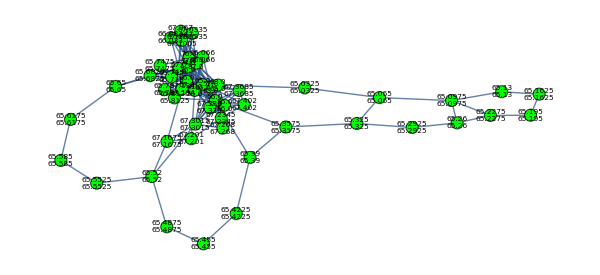

```mathematica
likelypairs=Extract[pairs,Position[liftvalues,x_/;x>1]];
Dimensions@likelypairs
AbsoluteTiming[binarymatrix=ArrayReshape[Table[If[j==True,1,0],{j,Table[MemberQ[likelypairs,i],{i,allmatrixelements}]}],{Length@binningmembers,Length@binningmembers}];]
graph=AdjacencyGraph[binarymatrix,{GraphLayout->Automatic,DirectedEdges->False,EdgeShapeFunction->"Line",VertexSize->1.5,VertexStyle->Green,VertexLabelStyle->Directive[Black,Italic,7.5],VertexLabels->Flatten[MapThread[{#1->Placed[#2,Center]}&,{Range[1,Dimensions[binarymatrix][[1]]],
Table[StringRiffle[i,"\n"],{i,binningmembers}]}]]},ImageSize->600]
```